```mathematica
L=1.1;
h=1;
```

```mathematica
texact[x_,y_]:={{Cos[2 π(x + 1.23 y)],Cos[4 π(x - y)]},{Sin[3 π (x+y/2)],Cos[2 π(x+y^2)]}}
```

```mathematica
t = Import ["/Users/michelecastellana/Desktop/t_sub_mesh.csv"]
```

```mathematica
t11=Table[{t[[i,10]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.,0.12533},{0.06875,-0.30154},{0.1375,-0.67301},{0.20625,-0.92085},{0.275,-0.99951},{0.34375,-0.89454},{0.4125,-0.62524},{0.48125,-0.24108},{0.55,0.18738},{0.61875,0.58141},{0.6875,0.86863},{0.75625,0.99627},{0.825,0.94088},{0.89375,0.71264},{0.9625,0.35347},{1.0312,-0.070627},{1.1,-0.48175}}

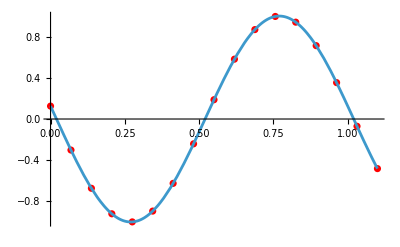

```mathematica
Show[ListPlot[t11,PlotStyle->Red],Plot[texact[x,h][[1,1]],{x,0,L}]]
```

```mathematica
t12=Table[{t[[i,10]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.,1.},{0.06875,0.64945},{0.1375,-0.15643},{0.20625,-0.85264},{0.275,-0.95106},{0.34375,-0.38268},{0.4125,0.45399},{0.48125,0.97237},{0.55,0.80902},{0.61875,0.078459},{0.6875,-0.70711},{0.75625,-0.99692},{0.825,-0.58779},{0.89375,0.23345},{0.9625,0.89101},{1.0312,0.92388},{1.1,0.30902}}

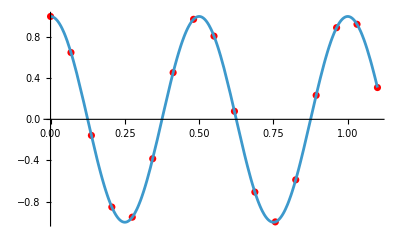

```mathematica
Show[ListPlot[t12,PlotStyle->Red],Plot[texact[x,h][[1,2]],{x,0,L}]]
```

```mathematica
t21=Table[{t[[i,10]],t[[i,4]]},{i,2,Length[t]}]
```

{{0.,-1.},{0.06875,-0.79732},{0.1375,-0.27144},{0.20625,0.36447},{0.275,0.85264},{0.34375,0.99518},{0.4125,0.73432},{0.48125,0.1758},{0.55,-0.45399},{0.61875,-0.89975},{0.6875,-0.98079},{0.75625,-0.66425},{0.825,-0.078459},{0.89375,0.53914},{0.9625,0.93819},{1.0312,0.95694},{1.1,0.58779}}

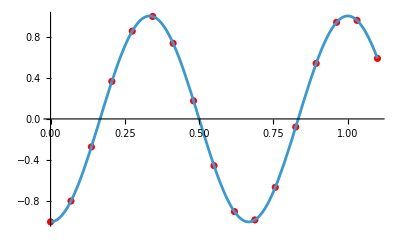

```mathematica
Show[ListPlot[t21,PlotStyle->Red],Plot[texact[x,h][[2,1]],{x,0,L}]]
```

```mathematica
t22=Table[{t[[i,10]],t[[i,5]]},{i,2,Length[t]}]
```

{{0.,1.},{0.06875,0.90814},{0.1375,0.64945},{0.20625,0.27144},{0.275,-0.15643},{0.34375,-0.55557},{0.4125,-0.85264},{0.48125,-0.99307},{0.55,-0.95106},{0.61875,-0.73432},{0.6875,-0.38268},{0.75625,0.03926},{0.825,0.45399},{0.89375,0.78532},{0.9625,0.97237},{1.0312,0.98079},{1.1,0.80902}}

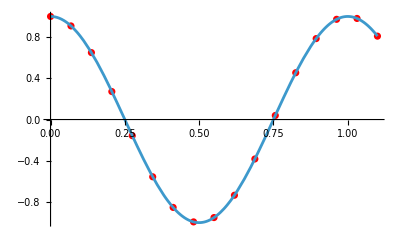

```mathematica
Show[ListPlot[t22,PlotStyle->Red],Plot[texact[x,h][[2,2]],{x,0,L}]]
```